```mathematica
SetDirectory[NotebookDirectory[]]
```

/media/akcays/8A83-9F10/Binary_NS_detection_Work

## LIGO L1 STRAIN during GW170817

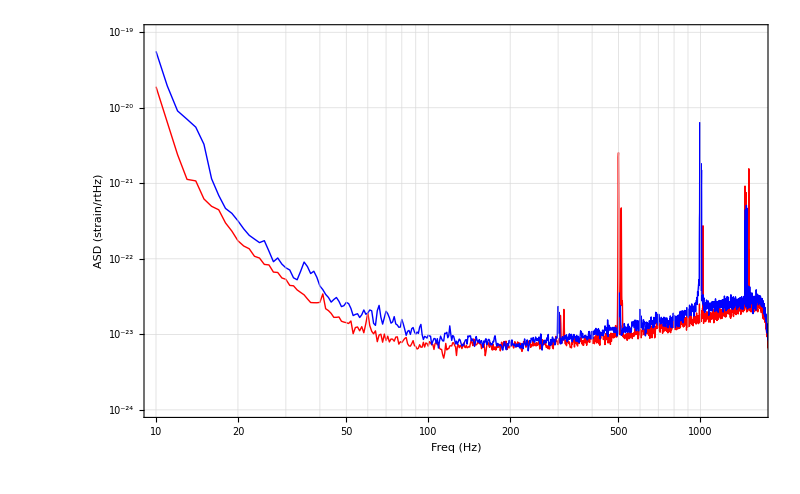

```mathematica
L1data="L-L1_LOSC_CLN_4_V1-1187007040-2048.hdf5";
H1data="H-H1_LOSC_CLN_4_V1-1187007040-2048.hdf5";
L1strain=SetPrecision[Import[L1data,{"Datasets","/strain/Strain"}],16];
H1strain=SetPrecision[Import[H1data,{"Datasets","/strain/Strain"}],16];
dt=1/4096;
(*L1attributes=Import[L1data,{"Attributes","/strain/Strain"}]
{t0,dtfloat,n}={"Xstart","Xspacing","Npoints"}/.L1attributes

dt-dtfloat
time=t0+(Range[n]-1) dt;*)
HannWindowTable=Table[HannWindow[(i-2048.5`16)/4096],{i,1,4096}];
MeanHann=Mean[Abs[Fourier[HannWindowTable]]^2];
AOL1specHann=Mean[Table[Abs[Fourier[L1strain[[1+4096 n;;4096 (n+1)]] HannWindowTable]]^2,{n,0,31}]]/MeanHann;
AOH1specHann=Mean[Table[Abs[Fourier[H1strain[[1+4096 n;;4096 (n+1)]] HannWindowTable]]^2,{n,0,31}]]/MeanHann;
L1ASD=Table[{i,Sqrt[2 dt AOL1specHann[[i+1]]]},{i,10,2000}];
H1ASD=Table[{i,Sqrt[2 dt AOH1specHann[[i+1]]]},{i,10,2000}];
GW170817L1ASDPlot=ListLogLogPlot[{L1ASD,H1ASD},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Red,Blue},FrameLabel->{"Freq (Hz)","ASD (strain/rtHz)"},PlotRange->{{10,1600},{10^-24,10^-19}},ImageSize->800]
```

## INTERPOLATING L1 GW170817 ASD and REMOVING BUMPS (not done)

```mathematica
L1ASDfit=Interpolation[L1ASD];
H1ASDfit=Interpolation[L1ASD];
```

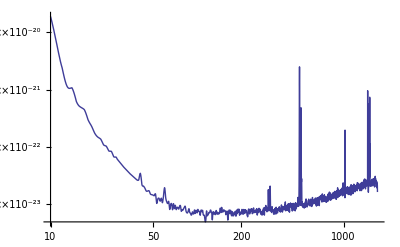

```mathematica
LogLogPlot[L1ASDfit[x],{x,10,1700}]
```

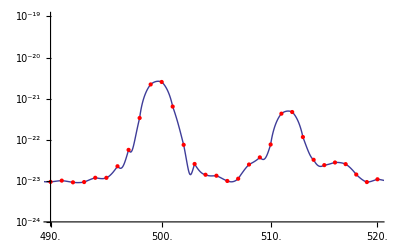

```mathematica
Show[LogLogPlot[L1ASDfit[x],{x,400,600},PlotRange->{{490,520},{10^-24,10^-19}}],ListLogLogPlot[L1ASD[[470;;520]],Frame->True,PlotStyle->{Red},FrameLabel->{"Freq (Hz)","ASD (strain/rtHz)"}]]
```

## DATA from A-LIGO BNS Optimized, Einstein Telescope B Low-frequency end

#### ASD = 2 h̃(f) √f where h̃(f) is the Fourier transform of h(t)

```mathematica
ALIGO2017Data={{7*10^5,6000,100,20,4,2,1,0.9,0.8,0.9,1,2,4}*10^-23,{9,10,15,20,30,40,70,80,100,200,400,1000,1200}};
ALIGODesigndata={{10^5,10^4,100,32,20,8,5,2.35,1,0.6,0.4,0.3,0.25,0.3,0.8,3}*10^-23,{6,7,9,9.7,10,11.89,14,20,30,40,60,200,300,400,900,1200}};
ETdata={{10^6,500,(*50,40,20,*)14,6,3,2,1,0.5,0.15,0.06,0.03,0.025,0.03,0.07,0.13,0.2}*10^-23,{0.5,1,(*1.2,1.3,1.5,*)2,3,4,5,7,10,20,30,60,150,300,1000,2000,3000}};
data={ALIGO2017Data,ALIGODesigndata,ETdata};
choice=3;
Ls=Table[Length[data[[i,1]]],{i,1,3}]
```

{13,16,16}

```mathematica
ThreeIFOData=Table[{data[[j,2,i]],data[[j,1,i]]},{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
GWFreqs=Table[ThreeIFOData[[j,i,1]],{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
ASDData=Table[ThreeIFOData[[j,i,2]],{j,1,Length[data]},{i,1,Ls[[j]]}];
```

```mathematica
ASDvFreqData=Table[{GWFreqs[[j,i]],ASDData[[j,i]]},{j,1,Length[data]},{i,1,Ls[[j]]}];
```

## BETTER ASD DATA using ONLINE SOFTWARE

```mathematica
ReadBNSData=Import["BNS_data_Read.csv","Data"];
RealisticBNSData=Sort[ReadBNSData];
```

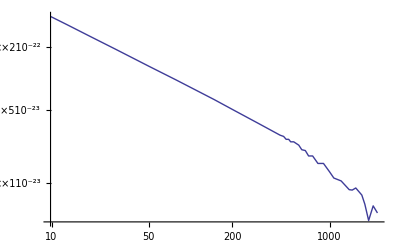

```mathematica
ListLogLogPlot[RealisticBNSData,Joined->True]
```

```mathematica
TextSize=22;
ALIGO2020Data=Join[{ASDvFreqData[[2,1]]},Sort[Import["ALIGO2020.csv","Data"]]];
ETBData=Sort[Import["ET_B.csv","Data"]];
ETCData=Sort[Import["ET_C.csv","Data"]];
```

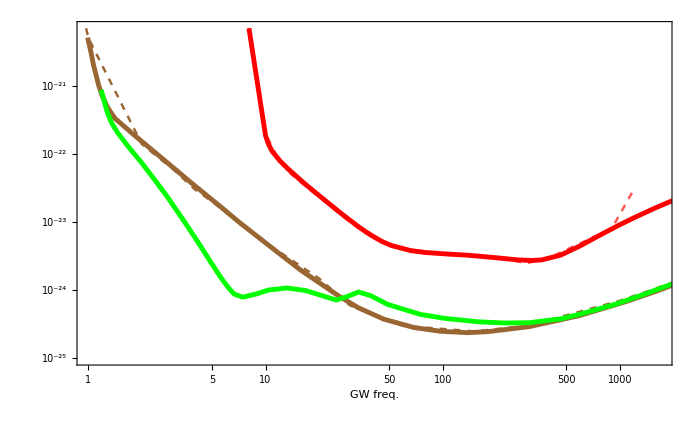

Figures/All_IFO_strains.pdf

```mathematica
IFOASDs=ListLogLogPlot[{ASDvFreqData[[2]],ASDvFreqData[[3]],ALIGO2020Data,ETBData,ETCData},PlotRange->{{1,1700},{10^-25,7 10^-21}},Joined->True,PlotStyle->{Directive[{Thickness[0.0025],Dashed,Lighter[Red]}],{Thickness[0.0025],Dashed,Brown},{Thickness[0.005],Red},{Thickness[0.005],Brown},{Thickness[0.005],Green}},AxesLabel->{"GW freq.",None},ImageSize->700,Frame->True,FrameStyle->Thick,FrameTicksStyle->24,Epilog->Inset[Framed[Column[{LineLegend[{Directive[{Thickness[0.125],Dashed,Lighter[Red]}],{Thickness[0.125],Dashed,Brown},{Thickness[0.25],Red},{Thickness[0.25],Brown},{Thickness[0.25],Green}},{Style["Old A-LIGO2020 Data",TextSize],Style["Old ET-B Data",TextSize],Style["New A-LIGO2020",TextSize],Style["New ET-B",TextSize],Style["ET-C",TextSize]}]}],RoundingRadius->5,FrameStyle->Directive[Black,AbsoluteThickness[4]],Background->White],Scaled[{0.75,0.75}]]]
Export["Figures/All_IFO_strains.pdf",IFOASDs]
```

## Preliminaries

```mathematica
Clear[x,h]
```

```mathematica
X=(G M Ω/c^3)^(2/3);
Msun=1.989*10^30;
clight=299792458;
Ggrav=6.67*10^-11;
ν=1/4;
Mc=ν^(3/5)M;
fISCO=c^3/(6^(3/2)π G M);
AngAveFact=1/Pi Integrate[(1+Cos[i]^2)/2,{i,0,Pi}];
Mpc=10^6*360/(2π)*3600*149597870700.;
GWfreqIsco=fISCO/.G->6.67*10^-11/.M->(2.8Msun)/.c->clight
fISCOGW170817=Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},fISCO]
Mtot=2.8 Msun;
```

1570.97

1605.37

## MERGER RATES

```mathematica
R={1540,1540+3200,1540-1220}
```

{1540,4740,320}

```mathematica
R*(40./1000)^3
```

{0.09856,0.30336,0.02048}

## AVERAGING of the ANTENNA PATTERNS

```mathematica
InclinationAv=2Pi 1/(4Pi)Integrate[(((1+Cos[i]^2)/2)^2+Cos[i]^2)Sin[i],{i,0,-Pi,Pi}]
```

4/5

```mathematica
Fplus=1/2(1+Cos[θ]^2)Cos[2ϕ]Cos[2ψ]-Cos[θ]Sin[2ϕ]Sin[2ψ];
Fx=1/2(1+Cos[θ]^2)Cos[2ϕ]Sin[2ψ]+Cos[θ]Sin[2ϕ]Cos[2ψ];
```

```mathematica
Fplus/.ψ->0/.ϕ->0/.θ->0
```

1

```mathematica
(*Average over θ,ϕ,ψ*)
1/(8 Pi^2)Integrate[Fplus^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
1/(8 Pi^2)Integrate[Fx^2*Sin[θ],{θ,0,Pi},{ϕ,0,2π},{ψ,0,2π}]
LowAv=√(1/5 InclinationAv)
```

1/5

1/5

2/5

```mathematica
(*Set ψ=0, average over θ,ϕ*)
1/(4Pi)Integrate[Fplus^2*Sin[θ]/.ψ->0,{θ,0,Pi},{ϕ,0,2π}]
1/(4Pi)Integrate[Fx^2*Sin[θ]/.ψ->0,{θ,0,Pi},{ϕ,0,2π}]
MedAv=√(7/30+1/6)
```

7/30

1/6

√(2/5)

## FREQ-DOMAIN STRAINS

```mathematica
A=π^(-2/3)√(5/24);
hFDOld[f_,D_]=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},AngAveFact*A*√2 c/D(G Mc/c^3)^(5/6)f^(-7/6)];
hFDHigh[f_,D_]=Block[{G=6.67*10^-11,(*M=(2.8Msun),*)c=clight}, A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
hFDMed[f_,D_]=Block[{G=6.67*10^-11,(*M=(2.8Msun),*)c=clight},MedAv A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
hFDRMS[f_,D_]=Block[{G=6.67*10^-11,(*M=(2.8Msun),*)c=clight},LowAv A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
hFDVeryLow[f_,D_]=Block[{G=6.67*10^-11,(*M=(2.8Msun),*)c=clight},(2LowAv-MedAv) A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
```

(6.78875×10^-23 M^(5/6))/(D f^(7/6))

(4.29358×10^-23 M^(5/6))/(D f^(7/6))

(2.7155×10^-23 M^(5/6))/(D f^(7/6))

(1.13742×10^-23 M^(5/6))/(D f^(7/6))

## LIGO2017 COMPARISON

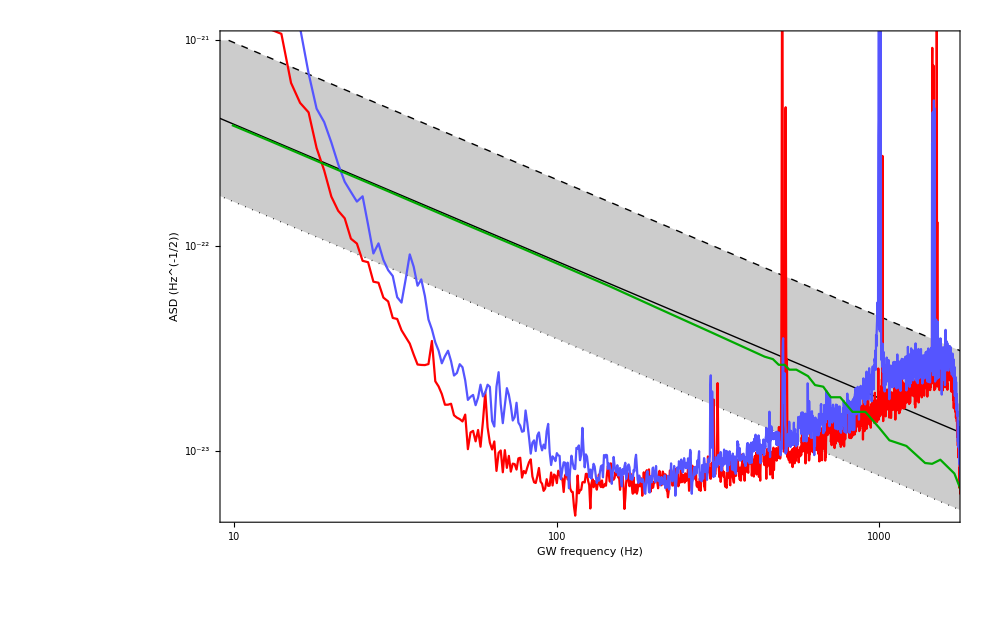

Figures/GW170817_strains.pdf

```mathematica
TextSize=22;
Block[{M=2.74Msun},FigGW170817=Show[LogLogPlot[{2 √f hFDHigh[f,40Mpc],(*2 √f hFDMed[f,40Mpc],*)2 √f hFDRMS[f,40Mpc],2 √f hFDVeryLow[f,40Mpc]},{f,1,2000},PlotStyle->{(*{Gray,Opacity[0.2]},*){Black,Dashed,Thick},{Thick,Black},{Black,Dotted,Thick},{Gray,Opacity[0]}},
Filling->{1->{3}}(*},{2->{4}}}*),FillingStyle->{{Directive[Black,Opacity[0.25]]}},PlotRange->{{10,fISCOGW170817},{5 10^-24,10^-21}}],
(*Graphics[Line[{{Log[fISCOGW170817],Log[10^-24]},{Log[fISCOGW170817],Log[10^-21]}}]],*) (* plots ISCO vertically *)
ListLogLogPlot[{L1ASD,H1ASD,RealisticBNSData},Joined->True,PlotStyle->{Red,{Lighter[Blue]},Darker[Green]},AxesLabel->{"GW freq.",None},PlotRange->{All,All}],ImageSize->1000,
Frame->True,FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["GW frequency (Hz)",24],Style["ASD (Hz^(-1/2))",24]},ImageSize->1000,Epilog->Inset[Framed[Column[{LineLegend[{Directive[Red,AbsoluteThickness[3]],Directive[Lighter[Blue],Thickness[0.005]],Directive[Black,Dashed,Thickness[0.005]],Directive[Black,Thickness[0.005]],Directive[Black,Dotted,Thickness[0.005]]},{Style["L1 during GW170817",TextSize],Style["H1 during GW170817",TextSize],Style["2√f(H̃)_h(f)",TextSize],Style["2√f(H̃)_m(f)",TextSize],Style["2√f(H̃)_l(f)",TextSize]}]}],RoundingRadius->5,FrameStyle->Directive[Black,AbsoluteThickness[4]],Background->White],Scaled[{0.8375,0.8375}]],FrameTicks->{{{{Log[10^-21],"10^-21"},{Log[10^-22],"10^-22"},{Log[10^-23],"10^-23"},{Log[5 10^-22],"5x10^-21"},{Log[5 10^-23],"5x10^-23"}},None},{{{Log[10],"10"},{Log[50],"50"},{Log[100],"100"},{Log[500],"500"},{Log[1000],"1000"}},None}},FrameTicksStyle->24]]
Export["Figures/GW170817_strains.pdf",FigGW170817]
```

## DEFINE THE SNR

### INTERPOLATE ASD DATA

```mathematica
Snoise=Table[Interpolation[ASDvFreqData[[i]],InterpolationOrder->1],{i,1,Length[data]}];
```

### CONSTRUCT the SNR

```mathematica
SNROld[i_,fi_,ff_,D_]:=(NIntegrate[4 hFDOld[f,D]^2/(Snoise[[i]][f])^2,{f,fi,ff}])^(1/2)
SNR2017High[fi_,ff_,D_]:=(NIntegrate[4 hFDHigh[f,D]^2/(L1ASDfit[f])^2,{f,fi,ff}])^(1/2)
SNR2017Med[fi_,ff_,D_]:=(NIntegrate[4 hFDMed[f,D]^2/(L1ASDfit[f])^2,{f,fi,ff}])^(1/2)
SNR2017RMS[fi_,ff_,D_]:=(NIntegrate[4 hFDRMS[f,D]^2/(L1ASDfit[f])^2,{f,fi,ff}])^(1/2)
SNR2017VeryLow[fi_,ff_,D_]:=(NIntegrate[4 (2hFDRMS[f,D]-hFDMed[f,D])^2/(L1ASDfit[f])^2,{f,fi,ff}])^(1/2)
SNRMax[i_,fi_,ff_,D_]:=(NIntegrate[4 hFDHigh[f,D]^2/(Snoise[[i]][f])^2,{f,fi,ff}])^(1/2)
SNR65[i_,fi_,ff_,D_]:=(NIntegrate[4 hFDMed[f,D]^2/(Snoise[[i]][f])^2,{f,fi,ff}])^(1/2)
SNRRMS[i_,fi_,ff_,D_]:=(NIntegrate[4 hFDRMS[f,D]^2/(Snoise[[i]][f])^2,{f,fi,ff}])^(1/2)
SNRLow[i_,fi_,ff_,D_]:=(NIntegrate[4 (2hFDRMS[f,D]-hFDMed[f,D])^2/(Snoise[[i]][f])^2,{f,fi,ff}])^(1/2)
```

## Inspiral time, accumulated phase: 0PN to 3.5PN expressions

```mathematica
Tinsp0PN[f0_,Mch_]=5/(256 π^(8/3))  (c^3/(G Mch))^(5/3) f0^(-8/3)/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;
Phi0PN[f0_,Mch_,M_]=2 (5 G Mch/c^3)^(-5/8) Tinsp0PN[f0,Mch]^(5/8)/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;
Ncycles0PN[f0_,Mch_,M_]=1/(32 π^(8/3)) (G Mch/c^3)^(-5/3) (f0^(-5/3)-fISCO^(-5/3))/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;

(*2PN expressions from Section 5.6.4 of Maggiore's Book*)

τ0[f_,M_]:=5/(256 ν f π) (π G M/c^3 f)^(-5/3)/.G->6.67*10^-11/.c->clight;
τ1[f_,M_]:=5/(192 ν f π) (π G M/c^3 f)^-1 (743/336+11/4 ν)/.G->6.67*10^-11/.c->clight;
τ15[f_,M_]:=1/(8 ν f) (π G M/c^3 f)^(-2/3)/.G->6.67*10^-11/.c->clight;
τ2[f_,M_]:=5/(128 ν f π) (π G M/c^3 f)^(-1/3) (3058673/1016064+5429/1008 ν+617/144 ν^2)/.G->6.67*10^-11/.c->clight;


Tinsp2PN[f_,fin_,M_]:=τ0[fin,M] (1-(f/fin)^(-8/3))+τ1[fin,M] (1-(f/fin)^-2)-τ15[fin,M] (1-(f/fin)^(-5/3))+τ2[fin,M] (1-(f/fin)^(-4/3));
Phi2PN[f_,fin_,M_]:=16 π/5 fin (τ0[fin,M] (1-(f/fin)^(-5/3))+5/4 τ1[fin,M] (1-(f/fin)^-1)-25/16 τ15[fin,M] (1-(f/fin)^(-2/3))+5/2 τ2[fin,M] (1-(f/fin)^(-1/3)));
```

### 2+ PN from Blanchet’s Review Article

```mathematica
(* 3.5 PN non-spinning binary phase *)
K=SeriesCoefficient[X/.Ω-> π f,{f,0,2/3}];
Xvar[f_]=K f^(2/3);
(* x0 is an integration constant *)
phi[x_,x0_]=-x^(-5/2)/(32ν)(1+(3715/1008+55/12 ν)x-10 π x^(3/2)+(15293365/1016064+27145/1008 ν+3085/144 ν^2)x^2+(38645/1344-65/16 ν)π x^(5/2)Log[x/x0]+(12348611926451/18776862720-160/3 π^2-1712/21 EulerGamma-856/21 Log[16x]+(-15737765635/12192768+2255/48 π^2)ν+76055/6912 ν^2-127825/5184 ν^3)x^3+(77096675/2032128+378515/12096 ν-74045/6048 ν^2)π x^(7/2));
(* Accumulated phase from x1 to x2 = Φ[x1] - Φ[x2] *)
PhiAcc[x1_,x2_]=FullSimplify[phi[x1,x0]-phi[x2,x0]]/.Log[x1/x0]-Log[x2/x0]->Log[x1/x2];
```

### SOLVING x(Θ) = x(f=30Hz) for Θ gives us inspiral time

```mathematica
Clear[T]
(* Θ is a rescaled time variable where Δt = Subscript[t, coal]- t *)
Θ=ν c^3/(G M)(Δt)/5;
xoft[T_]=(1/4)T^(-1/4)(1+(743/4032+11/48 ν)T^(-1/4)-1/5 π T^(-3/8)+(19583/254016+24401/193536 ν+31/288 ν^2)T^(-1/2)+(-11891/53760+109/1920 ν)π T^(-5/8)+(-10052469856691/6008596070400+1/6 π^2+107/420 EulerGamma-107/3360 Log[T/256]+(3147553127/780337152-451/3072 π^2)ν-15211/442368 ν^2+25565/331776 ν^3)T^(-3/4)+(-113868647/433520640-31821/143360 ν+294941/3870720 ν^2)π T^(-7/8));
```

## CHECKS: GW170817 at LIGO 2017, use M = 2.74 M_Sun Swept from 30 Hz to~2000 Hz in 60 seconds and~3000 cycles with SNR=28.8 at L1

```mathematica
fin=30;
Th=Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin==0,{Δt,50}][[1,2]];
Ncyc3p5PN=-1/Pi Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},PhiAcc[Xvar[fin],Xvar[fISCOGW170817]]];
Ncyc2PN=Phi2PN[fISCOGW170817,fin,2.74Msun]/(2Pi);
Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[fISCOGW170817,fin,2.74Msun], "(2PN) ", Tinsp0PN[fin,1.188Msun] ,"(0 PN) "," seconds"]
Print["𝒩_cycles  = ",Ncyc3p5PN"(3.5 PN), ",Ncyc2PN"(2PN), ",Ncycles0PN[fin,1.188Msun,2.74Msun] ,"(0PN)"]
```

τ_insp = 56.6472(3.5PN), 56.7156(2PN) 55.9091(0 PN)  seconds

𝒩_cycles  = 2710.62 (3.5 PN), 2718.29 (2PN), 2680.1(0PN)

```mathematica
SNROld[1,fin,fISCOGW170817,40 Mpc];
(*Print["My original SNR computation: ", %]*)
SNRhigh2017=Block[{M=2.74Msun},SNR2017High[fin,fISCOGW170817,40 Mpc]]//Quiet;
SNRmed2017=Block[{M=2.74Msun},SNR2017Med[fin,fISCOGW170817,40 Mpc]]//Quiet
SNRRMS2017=Block[{M=2.74Msun},SNR2017RMS[fin,fISCOGW170817,40 Mpc]]//Quiet;
SNRverylow2017=Block[{M=2.74Msun},SNR2017VeryLow[fin,fISCOGW170817,40 Mpc]]//Quiet;
Print["SNR(30Hz -> f_ISCO): ρ_h = ",SNRhigh2017," (optimal orientation), ρ_m= ",SNRRMS2017,"(RMS average), ρ_l = ",SNRverylow2017," (1σ from RMS)"]
ρtotGW170817=√(SNRhigh2017^2+SNRverylow2017^2+SNRRMS2017^2);
Print["ρ_tot = ",ρtotGW170817," (3 IFOs)" ](* vs. ", √(SNRhigh2017^2), "  (using Subscript[ρ, virgo] = 2 instead of Subscript[ρ, l])"]*)
```

22.6681

SNR(30Hz -> f_ISCO): ρ_h = 35.8414 (optimal orientation), ρ_m= 14.3366(RMS average), ρ_l = 6.00503 (1σ from RMS)

ρ_tot = 39.0666 (3 IFOs)

## FUTURE DETECTORS and SOURCES

```mathematica
M=2.8Msun;
```

### LEGEND

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

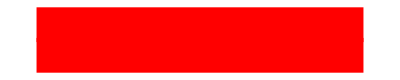
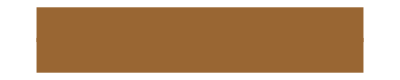
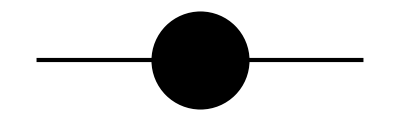

```mathematica
col={Red,Brown,Black};
col2={Blue,Darker[Green],Black,Gray}
legmarkers1=MapThread[Graphics[{#1,AbsoluteThickness[3],Line[{{-1,0},{1,0}}],#2}]&,{col,{Rectangle[{-1,-0.1},{1,0.1}],Rectangle[{-1,-0.1},{1,0.1}],Disk[{0,0},0.3]}}]
```

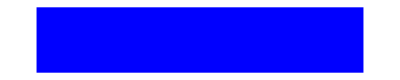
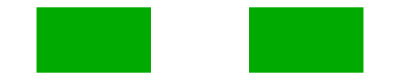
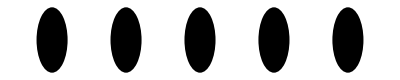
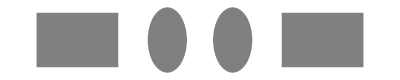

```mathematica
legmarkers2=MapThread[Graphics[{#1,AbsoluteThickness[3],#2}]&,{col2,{Rectangle[{-1,-0.1},{1,0.1}],{Rectangle[{-1,-0.1},{-.3,0.1}],Rectangle[{0.3,-0.1},{1,0.1}]},{Disk[{1/3,0},0.07],Disk[{0,0},0.07],Disk[{-1/3,0},0.07],Disk[{-2/3,0},0.07],Disk[{2/3,0},0.07]},{Rectangle[{-1,-0.1},{-.5,0.1}],Disk[{0.2,0},0.12],Disk[{-0.2,0},0.12],Rectangle[{0.5,-0.1},{1,0.1}]}}}]
```

```mathematica
legmarkers=Flatten[{legmarkers1,legmarkers2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### A-LIGO ET-B COMBINED PLOT

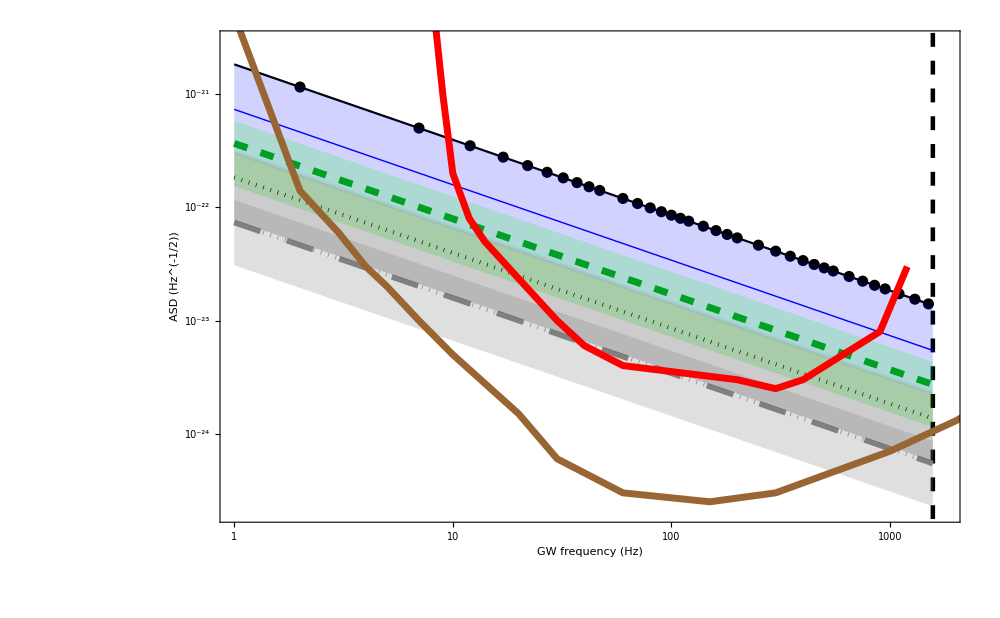

Figures/ALigo_ETB_strains.pdf

```mathematica
ASDPlots=Show[ListLogLogPlot[Table[{f,2 √f hFDRMS[f,40Mpc]},{f,2,50,5}],PlotStyle->{Black,PointSize[0.008]},PlotRange->{{1,1800},{2 10^-25,3 10^-21}}],
ListLogLogPlot[Table[{f,2 √f hFDRMS[f,40Mpc]},{f,60,110,10}],PlotStyle->{Black,PointSize[0.008]}],
ListLogLogPlot[Table[{f,2 √f hFDRMS[f,40Mpc]},{f,120,200,20}],PlotStyle->{Black,PointSize[0.008]}],
ListLogLogPlot[Table[{f,2 √f hFDRMS[f,40Mpc]},{f,250,500,50}],PlotStyle->{Black,PointSize[0.008]}],
ListLogLogPlot[Table[{f,2 √f hFDRMS[f,40Mpc]},{f,550,1000,100}],PlotStyle->{Black,PointSize[0.008]}],
ListLogLogPlot[Table[{f,2 √f hFDRMS[f,40Mpc]},{f,1100,1600,200}],PlotStyle->{Black,PointSize[0.008]}],
LogLogPlot[{2 √f hFDRMS[f,40Mpc],2 √f hFDRMS[f,100Mpc],2 √f hFDRMS[f,200Mpc],2 √f hFDRMS[f,400Mpc],2 √f hFDRMS[f,1000Mpc],2 √f hFDRMS[f,1000Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Black},{Blue,Thick},{Darker[Green],Thickness[0.005],Dashing[0.01]},{Black,Thickness[0.003],Dotted},{Gray,Thickness[0.004],Dashing[0.02]},{Gray,Thickness[0.003],Dotted}},PlotRange->{{1,1800},{2 10^-25,3 10^-21}}],
LogLogPlot[{2 √f hFDHigh[f,100Mpc],2 √f hFDVeryLow[f,100Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Blue,Opacity[0]},{Blue,Opacity[0]}},Filling->{1->{2}},FillingStyle->Directive[{Blue,Opacity[0.175]}]],
LogLogPlot[{2 √f hFDMed[f,200Mpc],2 √f hFDVeryLow[f,200Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Green,Opacity[0]},{Green,Opacity[0]}},Filling->{1->{2}},FillingStyle->Directive[{Green,Opacity[0.175]}]],
(* used the adhoc 2.12 in the plot below to hide an annoying white line in the middle of the shaded region that appears due to contrasts*)
LogLogPlot[{2.12 √f hFDMed[f,400Mpc],2 √f hFDVeryLow[f,400Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Thickness[0.003],Blue,Opacity[0.05]},{Black,Opacity[0]}},Filling->{1->{2}},FillingStyle->Directive[{Black,Opacity[0.2]}]],
LogLogPlot[{2 √f hFDMed[f,1000Mpc],2 √f hFDVeryLow[f,1000Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Gray,Opacity[0]},{Gray,Opacity[0]}},Filling->{1->{2}},FillingStyle->Directive[{Gray,Opacity[0.25]}]],
Graphics[{Black,Thickness[0.00325],Dashing[0.01],Line[{{Log[GWfreqIsco],Log[10^-25]},{Log[GWfreqIsco],Log[10^-20]}}]}],ListLogLogPlot[{ASDvFreqData[[2]],ASDvFreqData[[3]]},PlotRange->{{1,GWfreqIsco},{2 10^-25,7 10^-21}},Joined->True,PlotStyle->{{Thickness[0.005],Red},{Thickness[0.005],Brown},{Thickness[0.005],Black}},AxesLabel->{"GW freq.",None}],ImageSize->1000,Frame->True,
FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["GW frequency (Hz)",24],Style["ASD (Hz^(-1/2))",24]},
FrameTicks->{{{{Log[10^-21],"10^-21"},{Log[10^-22],"10^-22"},{Log[10^-23],"10^-23"},{Log[ 10^-24],"10^-24"}(*,{Log[5 10^-23],"5x10^-23"}*)},None},{{{Log[2],"2"},{Log[5],"5"},{Log[10],"10"},{Log[50],"50"},{Log[100],"100"},{Log[500],"500"},(*{Log[1000],"1000"},*){Log[GWfreqIsco],"f_ISCO"}},None}},FrameTicksStyle->24,
Epilog->Inset[Framed[Column[{
(*PointLegend[Directive[Black],Style["test",20],LegendMarkers->legmarkers],*)PointLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Brown,AbsoluteThickness[5]],Directive[Black,Thickness[0.007]],Directive[Blue,Thickness[0.007]],Directive[Darker[Green],Thickness[0.007],Dashing[0.02]],Directive[Black,Thickness[0.007],Dotted],Directive[Gray,Thickness[0.007],DotDashed]},{Style["A-LIGO 2020",TextSize],Style["ET-B 2030",TextSize],Style["BNS at 40 Mpc",TextSize],Style["BNS at 100 Mpc",TextSize],Style["BNS at 200 Mpc",TextSize],Style["BNS at 400 Mpc",TextSize],Style["BNS at 1000 Mpc",TextSize]},LegendMarkers->legmarkers,LegendMarkerSize->{30,10}]}],(*FrameStyle->Directive[Black,AbsoluteThickness[5]],*)RoundingRadius->5,Background->White],Scaled[{0.83,0.8}]]]
Export["Figures/ALigo_ETB_strains.pdf",ASDPlots]
```

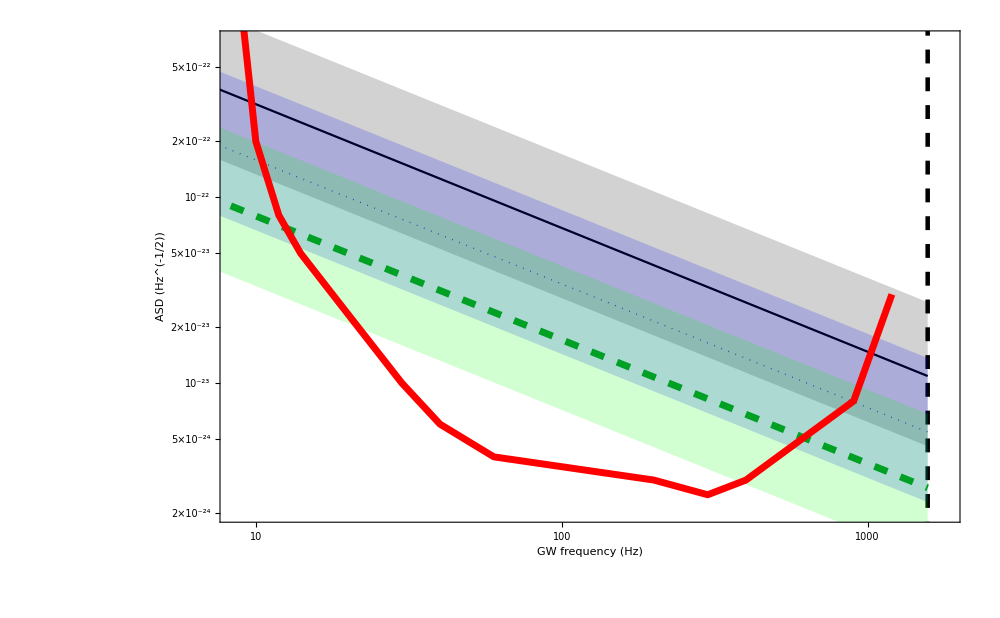

```mathematica
LIGOASDPlot=Show[
LogLogPlot[{2 √f hFDRMS[f,50Mpc],2 √f hFDRMS[f,100Mpc],2 √f hFDRMS[f,200Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Black},{Blue,Dotted,Thick},{Darker[Green],Thickness[0.005],Dashing[0.01]}},PlotRange->{{8.5,1800},{2 10^-24, 7 10^-22}}],
LogLogPlot[{2 √f hFDHigh[f,50Mpc],2 √f hFDVeryLow[f,50Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},Filling->{1->{2}},FillingStyle->Directive[{Black,Opacity[0.175]}]],
LogLogPlot[{2 √f hFDHigh[f,100Mpc],2 √f hFDVeryLow[f,100Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Blue,Opacity[0]},{Blue,Opacity[0]}},Filling->{1->{2}},FillingStyle->Directive[{Blue,Opacity[0.175]}]],
LogLogPlot[{2 √f hFDHigh[f,200Mpc],2 √f hFDVeryLow[f,200Mpc]},{f,1,GWfreqIsco},PlotStyle->{{Green,Opacity[0]},{Green,Opacity[0]}},Filling->{1->{2}},FillingStyle->Directive[{Green,Opacity[0.175]}]],
Graphics[{Black,Thickness[0.00325],Dashing[0.01],Line[{{Log[GWfreqIsco],Log[10^-25]},{Log[GWfreqIsco],Log[10^-20]}}]}],ListLogLogPlot[{ASDvFreqData[[2]]},Joined->True,PlotStyle->{{Thickness[0.005],Red},{Thickness[0.005],Brown},{Thickness[0.005],Black}},AxesLabel->{"GW freq.",None}],ImageSize->1000,Frame->True,
FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["GW frequency (Hz)",24],Style["ASD (Hz^(-1/2))",24]},
FrameTicks->{{{{Log[10^-21],"10^-21"},{Log[10^-22],"10^-22"},{Log[10^-23],"10^-23"},{Log[ 10^-24],"10^-24"},{Log[5 10^-23],"5x10^-23"},{Log[5 10^-22],"5x10^-22"},{Log[5 10^-24],"5x10^-24"}},None},{{{Log[2],"2"},{Log[5],"5"},{Log[10],"10"},{Log[20],"20"},{Log[50],"50"},{Log[100],"100"},{Log[200],"200"},{Log[500],"500"},{Log[1000],"1000"},{Log[GWfreqIsco],"f_ISCO"}},None}},FrameTicksStyle->24,
GridLines->{{Log[10],Log[20],Log[50],Log[100],Log[200],Log[500],Log[1000]},{Log[10^-23],Log[10^-22]}},
Epilog->Inset[Framed[Column[{
(*PointLegend[Directive[Black],Style["test",20],LegendMarkers->legmarkers],*)LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Black,Thickness[0.009]],Directive[Blue,Dotted,Thickness[0.007]],Directive[Darker[Green],Thickness[0.009],Dashing[0.02]]},{Style["A-LIGO 2020",TextSize],Style["BNS at 50 Mpc",TextSize],Style["BNS at 100 Mpc",TextSize],Style["BNS at 200 Mpc",TextSize]},(*LegendMarkers->{legmarkers[[1]],legmarkers[[5]],legmarkers[[4]],legmarkers[[5]]},*)LegendMarkerSize->{30,10}]}],(*FrameStyle->Directive[Black,AbsoluteThickness[5]],*)RoundingRadius->5,Background->White],Scaled[{0.8725,0.89}]]]
Export["Figures/ALigo_strains.pdf",LIGOASDPlot];
```

## A-LIGO 2020 Advance Warning Times, D=50, 100,200 Mpc

### A-LIGO entry frequencies f_0 for all 3 IFOs and and 2 sources

```mathematica
f0RootFinder[D_,fh_,fRMS_,fl_]:={2 √fh hFDHigh[fh,D]-Snoise[[2]][fh],2 √fRMS hFDRMS[fRMS,D]-Snoise[[2]][fRMS],2 √fl hFDVeryLow[fl,D]-Snoise[[2]][fl]}
```

```mathematica
f0={FindRoot[f0RootFinder[50Mpc,f1,f2,f3],{{f1,10},{f2,10},{f3,10}}][[All,2]],FindRoot[f0RootFinder[100Mpc,f1,f2,f3],{{f1,10},{f2,10},{f3,10}}][[All,2]],
FindRoot[f0RootFinder[200Mpc,f1,f2,f3],{{f1,10},{f2,10},{f3,10}}][[All,2]]}
```

{{9.16406,9.69605,11.2107},{9.61024,10.7727,13.7348},{10.0343,12.7801,23.4768}}

```mathematica
f0RMS=f0[[All,2]]
```

{9.69605,10.7727,12.7801}

### D = 40 Mpc

```mathematica
fbarRMS=20.43;
Block[{f=fbarRMS,D=40Mpc},(SNRMax[2,f0[[1,1]],f,D]^2+SNRRMS[2,f0[[1,1]],f,D]^2+SNRLow[2,f0[[1,1]],f,D]^2)^(1/2)]
fin=fbarRMS;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];
(*Ncyc3p5PN=-1/Pi Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},PhiAcc[Xvar[fin],Xvar[fISCOGW170817]]];
Ncyc2PN=Phi2PN[fISCOGW170817,fin,2.74Msun]/(2Pi);*)
Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[GWfreqIsco,fin,M], "(2PN) ", Tinsp0PN[fin,Mc] ,"(0 PN) "," seconds"]
ρtot=Block[{f=GWfreqIsco,D=40Mpc},(SNRMax[2,f0[[1,1]],f,D]^2+SNRRMS[2,f0[[1,1]],f,D]^2+SNRLow[2,f0[[1,1]],f,D]^2)^(1/2)];
Print["ρ_tot = ", ρtot]
```

15.0001

τ_insp = 151.926(3.5PN), 152.028(2PN) 149.25(0 PN)  seconds

ρ_tot = 101.223

### D = 50 Mpc

```mathematica
fbarRMS=23.37385;
Block[{f=fbarRMS,D=50Mpc},(SNRMax[2,f0[[1,1]],f,D]^2+SNRRMS[2,f0[[1,1]],f,D]^2+SNRLow[2,f0[[1,1]],f,D]^2)^(1/2)]
fin=fbarRMS;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];
(*Ncyc3p5PN=-1/Pi Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},PhiAcc[Xvar[fin],Xvar[fISCOGW170817]]];
Ncyc2PN=Phi2PN[fISCOGW170817,fin,2.74Msun]/(2Pi);*)
Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[GWfreqIsco,fin,M], "(2PN) ", Tinsp0PN[fin,Mc] ,"(0 PN) "," seconds"]
ρtot=Block[{f=GWfreqIsco,D=50Mpc},(SNRMax[2,f0[[1,1]],f,D]^2+SNRRMS[2,f0[[1,1]],f,D]^2+SNRLow[2,f0[[1,1]],f,D]^2)^(1/2)];
Print["ρ_tot = ", ρtot]
```

15.

τ_insp = 106.184(3.5PN), 106.273(2PN) 104.235(0 PN)  seconds

ρ_tot = 80.9781

### D = 100 Mpc

```mathematica
fbarRMS=36.90835;
Block[{f=fbarRMS,D=100Mpc},(SNRMax[2,f0[[1,1]],f,D]^2+SNRRMS[2,f0[[1,1]],f,D]^2+SNRLow[2,f0[[1,1]],f,D]^2)^(1/2)]
fin=fbarRMS;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];
(*Ncyc3p5PN=-1/Pi Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},PhiAcc[Xvar[fin],Xvar[fISCOGW170817]]];
Ncyc2PN=Phi2PN[fISCOGW170817,fin,2.74Msun]/(2Pi);*)
Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[GWfreqIsco,fin,M], "(2PN) ", Tinsp0PN[fin,Mc] ,"(0 PN) "," seconds"]
ρtot=Block[{f=GWfreqIsco,D=100Mpc},(SNRMax[2,f0[[1,1]],f,D]^2+SNRRMS[2,f0[[1,1]],f,D]^2+SNRLow[2,f0[[1,1]],f,D]^2)^(1/2)];
Print["ρ_tot = ", ρtot]
```

15.

τ_insp = 31.4651(3.5PN), 31.5201(2PN) 30.8293(0 PN)  seconds

ρ_tot = 40.4891

### D = 200 Mpc

```mathematica
fbarRMS=79.303;
Block[{f=fbarRMS,D=200Mpc},(SNRMax[2,f0[[1,1]],f,D]^2+SNRRMS[2,f0[[1,1]],f,D]^2+SNRLow[2,f0[[1,1]],f,D]^2)^(1/2)]
fin=fbarRMS;
Th=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Θ];
xin=Block[{G=6.67*10^-11,M=(2.8Msun),c=clight},Xvar[fin]];
Tinsp3p5PN=FindRoot[xoft[Th]-xin,{Δt,50}][[1,2]];
(*Ncyc3p5PN=-1/Pi Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},PhiAcc[Xvar[fin],Xvar[fISCOGW170817]]];
Ncyc2PN=Phi2PN[fISCOGW170817,fin,2.74Msun]/(2Pi);*)
Print["τ_insp = ",Tinsp3p5PN,"(3.5PN), ",Tinsp2PN[GWfreqIsco,fin,M], "(2PN) ", Tinsp0PN[fin,Mc] ,"(0 PN) "," seconds"]
ρtot=Block[{f=GWfreqIsco,D=200Mpc},(SNRMax[2,f0[[1,1]],f,D]^2+SNRRMS[2,f0[[1,1]],f,D]^2+SNRLow[2,f0[[1,1]],f,D]^2)^(1/2)];
Print["ρ_tot = ", ρtot]
```

15.

τ_insp = 4.08049(3.5PN), 4.10481(2PN) 4.01043(0 PN)  seconds

ρ_tot = 20.2445

## EINSTEIN TELESCOPE, amplitude scales down by √3/2

```mathematica
ETfact=√3/2;
```

## Scaling of Important Quantities in Terms of m_1, m_2

```mathematica
(* Mass ranges *)
R1={1,2}/Rationalize[1.4]
R2=R1;
```

{5/7,10/7}

```mathematica
Mchirp[m1_,m2_]:=(m1 m2)^(3/5)/(m1+m2)^(1/5);
ReducedMass[m1_,m2_]:=(m1 m2)/(m1+m2);
```

```mathematica
freq[m1_,m2_]:=(m1+m2)^(1/2);
fdot[m1_,m2_]:=Mchirp[m1,m2]^(5/3) freq[m1,m2]^(11/3);
Edot[m1_,m2_]:=ReducedMass[m1,m2]^2(m1+m2)^3;
FDstrain[m1_,m2_]:=Mchirp[m1,m2]^(5/6)(*freq[m1,m2]^(-7/6)*);
InspiralTime[m1_,m2_]:=1/(m1 m2 (m1+m2));
MergerFreq[m1_,m2_]:=1/(m1+m2);
```

```mathematica
Simplify[Edot[m1,m2],m1+m2>0]
Simplify[fdot[m1,m2],m1+m2>0]
InspiralTime[m1,m2]
Simplify[FDstrain[m1,m2],m1+m2>0]
```

m1^2 m2^2 (m1+m2)

m1 m2 (m1+m2)^(3/2)

1/(m1 m2 (m1+m2))

(√(m1 m2))/(m1+m2)^(1/6)

```mathematica
N[{Min[freq[R1,R2]],freq[1,1],Max[freq[R1,R2]]},3]
N[{Min[Edot[R1,R2]],Edot[1,1],Max[Edot[R1,R2]]},3]
N[{Min[fdot[R1,R2]],fdot[1,1],Max[fdot[R1,R2]]},3]
N[{Min[InspiralTime[R1,R2]],InspiralTime[1,1],Max[InspiralTime[R1,R2]]},3]
N[{Min[FDstrain[R1,R2]],FDstrain[1,1],Max[FDstrain[R1,R2]]},3]
N[{Min[MergerFreq[R1,R2]],MergerFreq[1,1],Max[MergerFreq[R1,R2]]},3]
N[{Min[InspiralTime[{1.2,1.6}/1.4,{1.2,1.6}/1.4]],InspiralTime[1,1],Max[InspiralTime[{1.2,1.6}/1.4,{1.2,1.6}/1.4]]},3]
N[{Min[FDstrain[{1.2,1.6}/1.4,{1.2,1.6}/1.4]],FDstrain[1,1],Max[FDstrain[{1.2,1.6}/1.4,{1.2,1.6}/1.4]]},3]
N[{Min[MergerFreq[{1.2,1.6}/1.4,{1.2,1.6}/1.4]],MergerFreq[1,1],Max[MergerFreq[{1.2,1.6}/1.4,{1.2,1.6}/1.4]]},6]
```

{1.2,1.41,1.69}

{0.372,2.,11.9}

{0.871,2.83,9.86}

{0.172,0.5,1.37}

{0.673,0.891,1.2}

{0.35,0.5,0.7}

{0.334961,0.5,0.793981}

{0.783501,0.891,0.995761}

{0.4375,0.5,0.583333}

## QUASI-CIRCULAR APPROXIMATION

```mathematica
Block[{M=2.8Msun},NSolve[96/5(Ggrav Mc)^(5/3)/clight^5 Ω^(5/3)==0.01,Ω]]
%[[1,1,2]]/Pi
```

{{Ω→1785.66}}

568.393

```mathematica
Block[{M=2.8Msun},NSolve[96/5(Ggrav Mc)^(5/3)/clight^5 Ω^(5/3)==0.001,Ω]]
%[[1,1,2]]/Pi
```

{{Ω→448.537}}

142.774

```mathematica
Block[{M=2.8Msun,Ω=Pi*200},96/5(Ggrav Mc)^(5/3)/clight^5 Ω^(5/3)]
```

0.00175375

## OCTUPOLE and CURRENT QUADRUPOLE

```mathematica
(*Kepler's law *)
```

```mathematica
ΩK=(√G √M)/r^(3/2);
```

```mathematica
v=r ΩK
```

(√G √M)/(√r)

```mathematica
Solve[Ω==ΩK,r][[1,1,2]]
```

1/(Ω/(√G √M))^(2/3)

```mathematica
Simplify[v^2/c^2/.r->Solve[Ω==ΩK,r][[1,1,2]]/.Ω->π f,G>0&&M>0]
%/.G->Ggrav/.c->clight/.M->2.8 Msun
v2c2=%/.f->100
Print["Mass octupole to quadrupole ratio at 100 Hz: ",25/896 v2c2,"\nMass octupole to current quadrupole ratio at 100 Hz: ",1215/896 v2c2]
1215/25.
```

((f G M)^(2/3) π^(2/3))/c^2

0.00123331 f^(2/3)

0.0265708

Mass octupole to quadrupole ratio at 100 Hz: 0.000741372
Mass octupole to current quadrupole ratio at 100 Hz: 0.0360307

48.6

## NEGLECTING NS SPIN

```mathematica
χ=Block[{M=1.4Msun,R=11000,Ii=2/5 M R^2},clight/Ggrav Ii/(1.4Msun)^2(2π)/10^-2]
```

0.049086

```mathematica
ScientificForm[4 Ggrav (100π)1.4 Msun χ/clight^3]
```

4.252×10^-4

## COSMOLOGY

```mathematica
z=0.25;
1571/(1+z)
```

1256.8

```mathematica
(1+z)^(5/3)
(1+z)^(5/6)
```

1.4505

1.20437